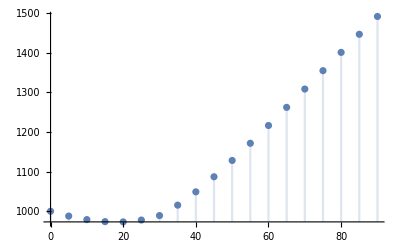

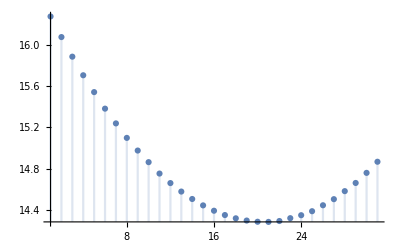

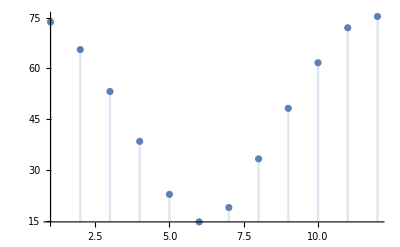

```mathematica
f:= Function[ (* params: hour of day, solar panel angle, date *)
sunPos = SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[#3,{#1}]];
(* remove degree unit, then convert to radians *)
Subscript[γ, s]= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
Subscript[γ, s] = Subscript[γ, s] - Pi;
Subscript[θ, s]= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
Subscript[γ, p] = 0; (* Solar panels azimuth *)
Subscript[θ, p] = #2 * Pi/180; (* Solar panels angle with horizontal *)
ArcCos[Cos[Subscript[γ, p]-Subscript[γ, s]] Cos[Subscript[θ, s]] Sin[Subscript[θ, p]]+Cos[Subscript[θ, p]] Sin[Subscript[θ, s]]]*180/Pi
]

(* Define a function that sums up the total of angles to the sun *)
g:=Function[ (* params: solar panel angle, date *)
position = GeoPosition[{51.546545,4.411744}];
sunUp = Sunrise[position,#2];
sunUpHour = DateValue[sunUp,"Hour"]+DateValue[sunUp, "Minute"]/60;
sunset = Sunset[position,#2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
Sum[f[h,#1,#2],{h,sunUpHour,sunsetHour}]
]

day := Function[ (* params: day of month, month *)
date = DateObject[{2016,#2,#1}];
(* Find for which angle of the solar panels this value is minimal *)
x /. FindMinimum[g[x,date],{x,0,0,90}, AccuracyGoal->5][[2]]
]
(* Graph for a specific day *)
date = DateObject[{2016,7,18}];
DiscretePlot[g[x,date],{x,0,90,5}]
(* Step of 0.5 takes 92 secs, 2 takes 27 secs, 5 takes ten seconds *)

(* Graph for a specific month *)
 DiscretePlot[day[a,6],{a,1,31}] (* Takes about ten seconds to complete *)

(* Find value for a specific month by taking the average *)
month := Function [ (* params: month *)
(* Count how many days are in this month *)
days = With[{first=DateObject[{2016,#1,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]] ;
Sum[day[x,#1],{x,1,days}]/days
]
DiscretePlot[month[x],{x,1,12}] (* Takes about 160 secs *)
```